# the workload test part 2

```mathematica
SetDirectory[NotebookDirectory[]];
rl[d_]:=Placed[d,Axis,Rotate[#,Pi/2]&]
SwapLoad[file_String]:=Import["../dataset/"<>file][[3;;All,5]]
VMLoad[file_String]:=Import["../dataset/"<>file][[4;;,{3,5,7}]];
```

## dynamic tau redo all test

### 3-8 dynamic tau

key | value | key | value
N | 5GB | init mem | 512MB
VM count | 10 | f | 150MB
high load | 200MB | □ | □

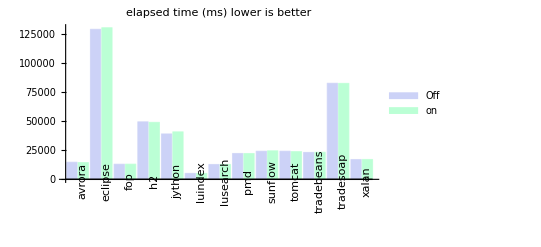

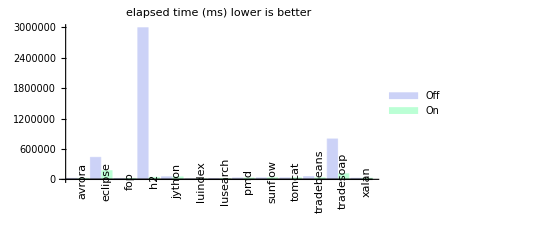

(ms) | off | on
avrora | 18238 | 17358
eclipse | 433186 | 171196
fop | 16029 | 17748
h2 | 2991145 | 37778
jython | 49847 | 47796
luindex | 6268 | 6144
lusearch | 15821 | 16029
pmd | 27475 | 26530
sunflow | 29067 | 30805
tomcat | 29034 | 29370
tradebeans | 54152 | 29416
tradesoap | 796455 | 110001
xalan | 21351 | 22948
sum | 4488068 | 563119

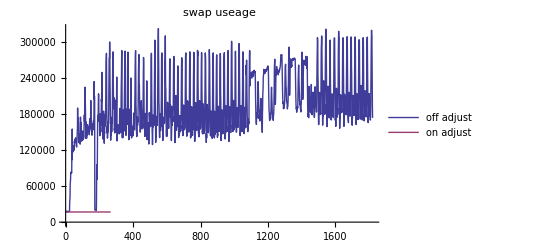

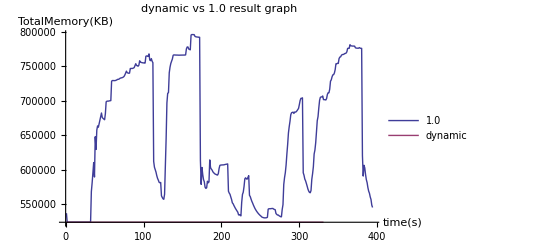

```mathematica
dp=Import["../dataset/3-8_dacapo/dacapo.ods"][[1]];
swapoff=SwapLoad["3-8_dacapo/off-swap.log"];
swapon=SwapLoad["3-8_dacapo/on-swap.log"];
hi=VMLoad["3-8_dacapo/high-2.log"];
low=VMLoad["3-8_dacapo/low-2.log"];
BarChart[dp[[2;;-2,2;;3]],
ChartLabels->{rl[dp[[2;;-2,1]]],None},
ChartLegends->{"Off","on"},PlotLabel->"elapsed time (ms) lower is better"]
BarChart[dp[[2;;-2,4;;5]],
ChartLabels->{rl[dp[[2;;-2,1]]],None},
ChartLegends->{"Off","On"},PlotLabel->"elapsed time (ms) lower is better"]
Grid[dp[[All,{1,4,5}]],Frame->All]
ListLinePlot[{swapoff,swapon},
PlotLabel->"swap useage",
PlotLegends->{"off adjust","on adjust"}]
ListLinePlot[{hi[[All,1]],low[[All,1]]},
PlotLegends->{"1.0","dynamic"},AxesLabel->{"time(s)","TotalMemory(KB)"},PlotLabel->"dynamic vs 1.0 result graph"]
Clear[dp,swapoff,swapon,hi,low]
```

配置512MB内存,运行时间相差非常大,而且几乎无法看到开启调节的柱状图.
而且SWAP分区使用率也是非常的夸张.
这个只能说是对于人而言.没有美观的感觉.但是对于系统而言是正常的结果.
我们需要接受它,当然.在论文中不使用这组数据.

### 3-9 dynamic tau high

key | value | key | value
N | 10GB | init mem | 1GB
VM count | 10 | f | 150MB
high load | 800MB | □ | □

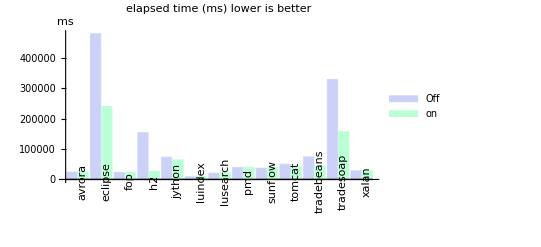

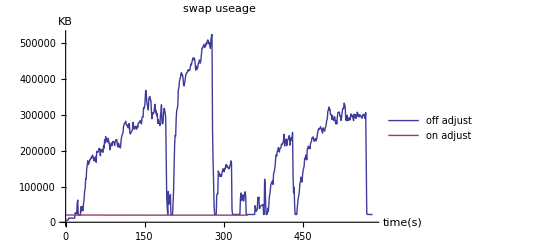

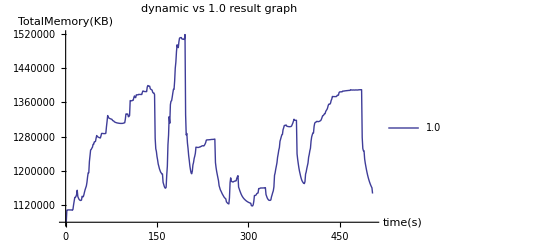

```mathematica
dp=Import["../dataset/3-9_dacapo_high/dacapo.ods"][[1]];
swapoff=SwapLoad["3-9_dacapo_high/off-swap.log"];
swapon=SwapLoad["3-9_dacapo_high/on-swap.log"];
hi=VMLoad["3-9_dacapo_high/high-10.log"];
BarChart[dp[[2;;-2,2;;3]],
ChartLabels->{rl[dp[[2;;-2,1]]],None},
ChartLegends->{"Off","on"},PlotLabel->"elapsed time (ms) lower is better",
AxesLabel->"ms"
]
ListLinePlot[{swapoff,swapon},
PlotLabel->"swap useage",AxesLabel->{"time(s)","KB"},
PlotLegends->{"off adjust","on adjust"}]
ListLinePlot[{hi[[All,1]]},
PlotLegends->{"1.0","dynamic"},AxesLabel->{"time(s)","TotalMemory(KB)"},PlotLabel->"dynamic vs 1.0 result graph"]
Clear[dp,swapoff,swapon,hi]
```

结论和以前的类似.

## multi vm test

### 测试方法

首先分为两个大组,一个大组是开启调节的测试,一个大组是关闭调节的测试.
每个大组安排每个虚拟机上运行不同性质的测试.为了保证满足调节条件.需要安排
每个大组至少有一台以上的vm运行内存密集程序,称为目标机.至少有一台以上的vm运行非内存密集程序
(如CPU密集和磁盘密集).为了使得运行非内存密集的vm把内存贡献给目标机.
同时,每台vm在测试的时候还需要执行记录swap的程序.在开启调节的时候需要记录每台虚拟机分配的内存.

内存型密集程序可以选择dacapo测试集中的h2,...因为目前只找到dacapo测试集的这几个测试属于内存密集型.
非内存密集型可以选择phoronix-test-suite测试框架中的许多程序如:
nginx
...

因为每个测试运行的时间都不一样.所以规定以单次测试时间最长的测试所运行的时间作为该大组测试的时间.
对于单次运行时间不足的测试采用循环运行的方式.当运行时间超过该大组的测试时间时候强制手工杀死测试进程.
因为杀死的该次测试成绩无效.对于之前运行的所有测试成绩(包括循环运行的所有有效成绩)取平均值作为该项测试的成绩.

最后将两大组的每个测试的成绩相除,换算成百分比.以不开启调节为基准1.因为一些测试成绩是越高越好,一些成绩是越低越好.
所以需要注意除以的方向

### 3-22 2vm test

N | 1G | init men | 512MB
vmcount | 2 | f | 120M
vm1 | nginx | high load | 0
vm2 | h2 | high load | 100MB

| vm1 | vm2
 | nginx | h2
unit | request/s | ms
off | 6589.78 | 110753
on | 6488.57 | 42207

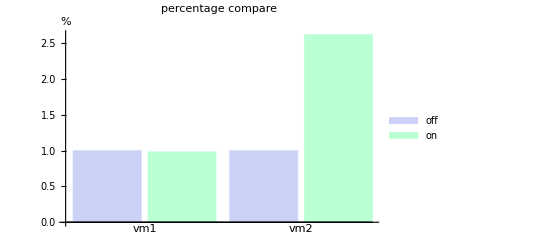

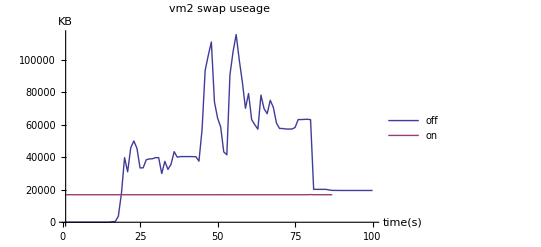

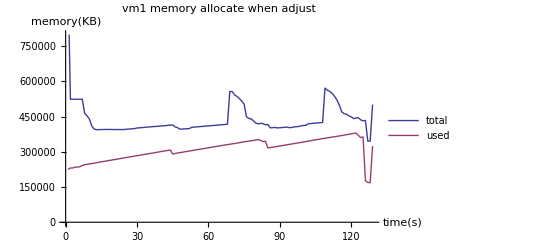

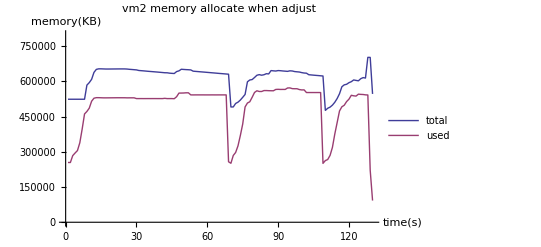

```mathematica
table=Import["../dataset/3-22/statics.ods"][[1]];
offswap={None,SwapLoad["3-22/vm2/off-swap.log"]};
onswap={SwapLoad["3-22/vm1/on-swap.log"],SwapLoad["3-22/vm2/on-swap.log"]};
onmem={VMLoad["3-22/vm1/on.log"],VMLoad["3-22/vm2/on.log"]};
Grid[table[[1;;-2]],Frame->All]
BarChart[{{1,table[[5,2]]/table[[4,2]]},{1,table[[4,3]]/table[[5,3]]}},
PlotLabel->"percentage compare",ChartLegends->{"off","on"},
ChartLabels->{{"vm1","vm2"},None},AxesLabel->"%"
]
ListLinePlot[{offswap[[2,1;;-40]],onswap[[2]]},
PlotRange->All,PlotLabel->"vm2 swap useage ",PlotLegends->{"off","on"},
AxesLabel->{"time(s)","KB"}
]
ListLinePlot[{onmem[[1,All,1]],onmem[[1,All,2]]},
PlotRange->{0,800000},PlotLabel->"vm1 memory allocate when adjust",
PlotLegends->{"total","used"},AxesLabel->{"time(s)","memory(KB)"}
]
ListLinePlot[{onmem[[2,All,1]],onmem[[2,All,2]]},
PlotRange->{0,800000},PlotLabel->"vm2 memory allocate when adjust",
PlotLegends->{"total","used"},AxesLabel->{"time(s)","memory(KB)"}
]
Clear[table,offswap,onswap,onmem]
```

对于两台虚拟机的测试,可以看到结果是类似的.主要依然表现为以下几个方面:
图1:
-    对于非内存密集型的程序.性能会有所下降.但是下降的数量不大.
-    对于内存密集型的程序.因为保证了分配足够的内存.所以相对于不开启调节的性能有提升许多
图2:
-    不开启调节的vm2占用大量的swap.(vm1因为不需要太多内存,所以始终没有使用swap).
-    开启了调节之后vm2就不再使用swap了.(从途中可以看到swap一直保持一个数,这是因为不开启调节的测试是紧接着上一个测试的)
-    两者运行的时间相差无几.这是因为整个测试以最长的时间为基准(vm1上单次运行需要的时间)
      vm2上其实完整的执行了2次
图3,图4:
-   对于vm1可以看到,分为3个阶段.其实是3次测试,phoronix-test-suite默认运行3次求平均值作为最后结果.
    三次测试内存需求逐渐升高.
-   对于vm2可以看到,分为2个完整的测试和一个不完整的测试.因为dacapo只运行1次.所以当第一次运行结束之后,
    就通过外部的脚本的循环,进行下一个周期,而且明显的可以看到第二次运行的时间比第一次短得多.关于这一点目前还没有能力解释.
    当第3次还没有运行完成之后.vm1就结束了.所以这里手工杀死测试进程.
    
2台虚拟机的测试还不能说明什么问题.
下面的5台虚拟机和10台虚拟机能够更加深刻的说明问题.